```mathematica
randomData=RandomReal[{0,1},100]
```

{0.304989,0.654415,0.721887,0.800153,0.926603,0.713492,0.0871934,0.276991,0.0444428,0.420944,0.676709,0.076037,0.475273,0.567986,0.955138,0.570602,0.148277,0.820875,0.447348,0.0628472,0.671778,0.772822,0.723177,0.43509,0.965288,0.0545449,0.234403,0.573772,0.78531,0.987124,0.293569,0.941757,0.794436,0.524133,0.800419,0.888588,0.0316406,0.227618,0.395067,0.106764,0.60047,0.622962,0.663204,0.820131,0.896463,0.516544,0.31809,0.899929,0.784956,0.491895,0.0447634,0.179223,0.147628,0.88374,0.903791,0.298349,0.843892,0.273755,0.922081,0.180703,0.579474,0.995333,0.233914,0.839714,0.274509,0.405965,0.602424,0.503839,0.905705,0.847508,0.185429,0.805564,0.37384,0.0372217,0.915279,0.186651,0.437974,0.754649,0.866255,0.218309,0.0735907,0.957292,0.265077,0.876158,0.207565,0.753612,0.243254,0.144901,0.190592,0.840168,0.966275,0.688566,0.155275,0.0132194,0.983989,0.893359,0.495192,0.581503,0.918573,0.0994786}

```mathematica
randomData={0.7244876507293305,0.21254284435450765,0.4780234432108086,0.11443386955331492,0.6039664341554787,0.7663785659934201,0.31433107401380367,0.0896320224454803,0.9829885646778,0.3017563296003858,0.6302241938228359,0.6616575618787137,0.6515864078306326,0.8749277137204305,0.4393075947438163,0.9929373663729424,0.01955271064167463,0.04785051103958282,0.3338684031071655,0.3668117590896518,0.012384501090589861,0.9044732740661434,0.9804470809965067,0.7336582996809082,0.6295784781460745,0.33005573418503054,0.14977783214194584,0.9395053536503606,0.7221112918265102,0.997658013425424,0.9846687091506952,0.5627727561467333,0.9654332176436133,0.303848689737364,0.653747298172602,0.8265374053275463,0.03704773288123797,0.7605289694532416,0.9936058861394472,0.1963200550244919,0.5929892911316137,0.9889340037028582,0.46138224130685956,0.25588715321933786,0.8551959130290743,0.6290798614130959,0.028654656506267306,0.49898126066401116,0.5517502812791271,0.5078547662527049,0.30425822810257985,0.44377560397037064,0.4193753920332939,0.7976854249690912,0.0003690919930035008,0.9434650072644397,0.59161110117445,0.6543484130964672,0.23849822644290897,0.947128239075077,0.7051158841628415,0.7189921205094791,0.20095727756599557,0.5639412705817244,0.4190180780685009,0.013630686648675727,0.4049150766611238,0.226403559580727,0.38770599888438295,0.8464435533098393,0.7394960291670967,0.2609534008643588,0.3064198359468482,0.7693399337446349,0.8779039050405,0.9065841766180922,0.6166104758285762,0.5990060976332474,0.8891141589367166,0.03922990413607352,0.5887442174970303,0.7341448484748578,0.47198024052541276,0.08910770242712629,0.5141018237758437,0.1108675165504378,0.15267222657460366,0.9307399247164678,0.5166435987028033,0.8152266931844807,0.32501888247033506,0.11470114412167631,0.6247477807511139,0.6681142043935648,0.5285928430812497,0.612413667209512,0.3470486050201034,0.26213401124958846,0.23382745337614907,0.10757047736329595}
```

{0.724488,0.212543,0.478023,0.114434,0.603966,0.766379,0.314331,0.089632,0.982989,0.301756,0.630224,0.661658,0.651586,0.874928,0.439308,0.992937,0.0195527,0.0478505,0.333868,0.366812,0.0123845,0.904473,0.980447,0.733658,0.629578,0.330056,0.149778,0.939505,0.722111,0.997658,0.984669,0.562773,0.965433,0.303849,0.653747,0.826537,0.0370477,0.760529,0.993606,0.19632,0.592989,0.988934,0.461382,0.255887,0.855196,0.62908,0.0286547,0.498981,0.55175,0.507855,0.304258,0.443776,0.419375,0.797685,0.000369092,0.943465,0.591611,0.654348,0.238498,0.947128,0.705116,0.718992,0.200957,0.563941,0.419018,0.0136307,0.404915,0.226404,0.387706,0.846444,0.739496,0.260953,0.30642,0.76934,0.877904,0.906584,0.61661,0.599006,0.889114,0.0392299,0.588744,0.734145,0.47198,0.0891077,0.514102,0.110868,0.152672,0.93074,0.516644,0.815227,0.325019,0.114701,0.624748,0.668114,0.528593,0.612414,0.347049,0.262134,0.233827,0.10757}

```mathematica
Export[NotebookDirectory[]<>"04-random_data.dat",randomData]
```

/home/jam/Kuweta/mma_lessons/code/04-random_data.dat

```mathematica
randomData=Flatten[Import[NotebookDirectory[]<>"04-random_data.dat"]];
```

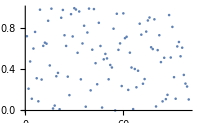

```mathematica
ListPlot[randomData,ImageSize->200]
```

```mathematica
Export[NotebookDirectory[]<>"pics/04-list_plot-random_data.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/04-list_plot-random_data.pdf

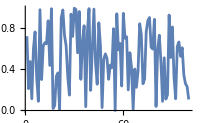

```mathematica
ListPlot[randomData,ImageSize->200,Joined->True]
```

```mathematica
Export[NotebookDirectory[]<>"pics/04-list_plot-random_data-joined.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/04-list_plot-random_data-joined.pdf

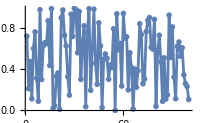

```mathematica
ListPlot[randomData,ImageSize->200,Joined->True,PlotMarkers->{"OpenMarkers"}]
```

```mathematica
Export[NotebookDirectory[]<>"pics/04-list_plot-random_data-joined-markers.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/04-list_plot-random_data-joined-markers.pdf

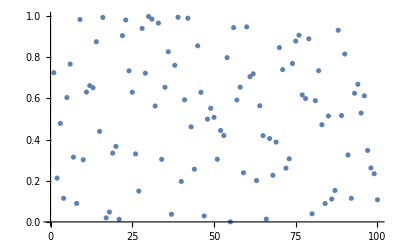

```mathematica
ListPlot[{Table[i,{i,Length[randomData]}],randomData}ᵀ]
```

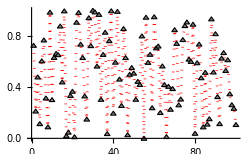

```mathematica
ListPlot[randomData,Joined->True,PlotStyle->Directive[Dotted,Red], ImageSize->250,
PlotMarkers->{
Graphics[{Gray,
EdgeForm[Black],
Triangle[{{0,0},{1,Sqrt[2]},{2,0}}]
}],
0.05}
]
```

```mathematica
Export[NotebookDirectory[]<>"pics/04-list_plot-random_data-custom-markers.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/04-list_plot-random_data-custom-markers.pdf

```mathematica
randomData[[1;;100;;10]]//Length
```

10

```mathematica
randomData[[91]]
```

0.325019

```mathematica
randomData[[1;;100;;10]][[-1]]
```

0.325019

```mathematica
ListPlot[randomData[[1;;100;;10]],
PlotRange->{0,1.2},ImageSize->275,
LabelingFunction->(If[0.5<=#1[[2]]<=0.75,
Callout[
#1[[2]],Above,
CalloutStyle->Blue,CalloutMarker->"BoxPoint"],
Callout[
#1[[2]],#1+{-0.2,0.075},
CalloutStyle->Red,CalloutMarker->"Star",
Appearance->"Balloon"
]
]&)
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/04-list_plot-random_data-labeling_function.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/04-list_plot-random_data-labeling_function.pdf